```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_AR_DLB_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_BR_DLB_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{{1.,1,1},{1.,1.,0.000341491},{1,1.,0.0000126478,0.000341491}},{{1.,1,1},{1.,1.,0.000436062},{1,1.,4.00793×10^-8,0.000436062}},{{0.00146843,1,681},{0.00119082,0.00146843,0.000277936},{0.682016,0.00146843,5.15678×10^-6,0.000277936}},{{0.00645161,1,155},{0.0061875,0.00645161,0.000265757},{0.921345,0.00645161,6.82174×10^-7,0.000265757}},{{0.00746269,5,670},{0.00703189,0.00746269,0.000433849},{0.890847,0.00746269,1.43745×10^-7,0.000433849}},{{0.00613497,5,815},{0.00580987,0.00613497,0.000326998},{0.899351,0.00613497,1.17189×10^-8,0.000326998}},{{0.028169,2,71},{0.0273054,0.028169,0.000887865},{0.940507,0.028169,1.03933×10^-10,0.000887865}},{{0.0344828,2,58},{0.0336203,0.0344828,0.000892412},{0.951201,0.0344828,1.24455×10^-11,0.000892412}},{{1.,1,1},{1.,1.,0.000435964},{1,1.,9.9865×10^-14,0.000435964}}}

{{{1.,160,160},{1.,1.,0.000436062},{1,1.,6.41268×10^-6,0.000436062}},{{1.,7,7},{1.,1.,0.000277936},{1,1.,5.30065×10^-8,0.000277936}},{{0.00146843,1,681},{0.00120299,0.00146843,0.000265757},{0.69382,0.00146843,2.99716×10^-6,0.000265757}},{{0.00645161,28,4340},{0.00617399,0.00645161,0.000279347},{0.917488,0.00645161,9.31121×10^-7,0.000279347}},{{0.00628931,78,12402},{0.00596426,0.00628931,0.000326998},{0.901714,0.00628931,1.78329×10^-7,0.000326998}},{{0.00452489,25,5525},{0.00431789,0.00452489,0.00020789},{0.912511,0.00452489,8.08775×10^-9,0.00020789}},{{0.00816327,2,245},{0.00727735,0.00816327,0.000892412},{0.804199,0.00816327,5.25713×10^-11,0.000892412}},{{0.0344828,2,58},{0.0336171,0.0344828,0.000895731},{0.951024,0.0344828,5.79217×10^-12,0.000895731}}}

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{1.,1.,0.00146843,0.00645161,0.00746269,0.00613497,0.028169,0.0344828,1.}

{1.,1.,0.00119082,0.0061875,0.00703189,0.00580987,0.0273054,0.0336203,1.}

{1,1,0.682016,0.921345,0.890847,0.899351,0.940507,0.951201,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{1.,1.,0.00146843,0.00645161,0.00628931,0.00452489,0.00816327,0.0344828}

{1.,1.,0.00120299,0.00617399,0.00596426,0.00431789,0.00727735,0.0336171}

{1,1,0.69382,0.917488,0.901714,0.912511,0.804199,0.951024}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={0,1,2,3,4,5,6,7,8};
sList2={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran]
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&,ran2];
```

{{0,1.},{1,1.},{2,0.00146843},{3,0.00645161},{4,0.00746269},{5,0.00613497},{6,0.028169},{7,0.0344828},{8,1.}}

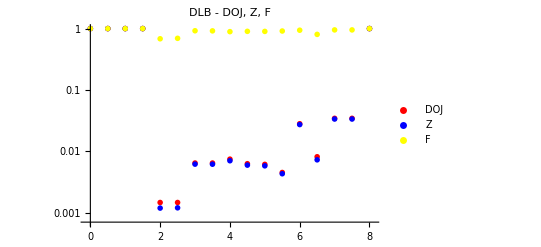

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"DLB - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/DLB/"];
Put[Union[dojPAR,dojPBR],"DLB_DOJ.txt"]
Put[Union[zPAR,zPBR],"DLB_Z.txt"]
Put[Union[fPAR,fPBR],"DLB_F.txt"]
Export["DLB.jpeg",PlotAllParts,ImageSize->800, ImageResolution->300]
```

DLB.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"DLB - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["DLB_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```